## Зададим необходимые функции

```mathematica
ClearAll[Ffor1,r2for1,φfor1,Xfor1,Yfor1];
```

```mathematica
Ffor1[n_,r1_,r2_]:=1/((n-1)(r2-r1));
r2for1[n_,r1_,F_] := 1/(F(n-1))+r1;
φfor1[n0_,r_,φin_,y_]:=ArcSin[n0 Sin[φin-ArcSin[y r]]]+ArcSin[y r];
Xfor1[F_,φout_,y_]:=2F -y 1/Tan[-φout];
Yfor1[F_,φout_,y_]:=2F Tan[-φout]-y;
F0=40;n=1.5;H=10;
Xfor1[F0,φfor1[n,r2for1[n,r1,F0],φfor1[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2]
```

80+5 Cot[ArcSin[5 (0.05+r1)]+ArcSin[1.5 Sin[ArcSin[5 r1]-ArcSin[5 (0.05+r1)]-ArcSin[0.666667 Sin[ArcSin[5 r1]-ArcTan[1/16]]]]]]

```mathematica
F0=80;n=1.5;H=10;
Xfor1[F0,φfor1[n,r2for1[n,r1,F0],φfor1[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2]
```

160+5 Cot[ArcSin[5 (0.025+r1)]+ArcSin[1.5 Sin[ArcSin[5 r1]-ArcSin[5 (0.025+r1)]-ArcSin[0.666667 Sin[ArcSin[5 r1]-ArcTan[1/32]]]]]]

```mathematica
F0=40;n=1.5;H=15;
Xfor1[F0,φfor1[n,r2for1[n,r1,F0],φfor1[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2]
```

80+15/2 Cot[ArcSin[15/2 (0.05+r1)]+ArcSin[1.5 Sin[ArcSin[(15 r1)/2]-ArcSin[15/2 (0.05+r1)]-ArcSin[0.666667 Sin[ArcSin[(15 r1)/2]-ArcTan[3/32]]]]]]

```mathematica
F0=40;n=2;H=10;
Xfor1[F0,φfor1[n,r2for1[n,r1,F0],φfor1[1/n,r1,ArcTan[H/(4 F0)],H/2],H/2],H/2]
```

80+5 Cot[ArcSin[5 (1/40+r1)]+ArcSin[2 Sin[ArcSin[5 r1]-ArcSin[5 (1/40+r1)]-ArcSin[1/2 Sin[ArcSin[5 r1]-ArcTan[1/16]]]]]]

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

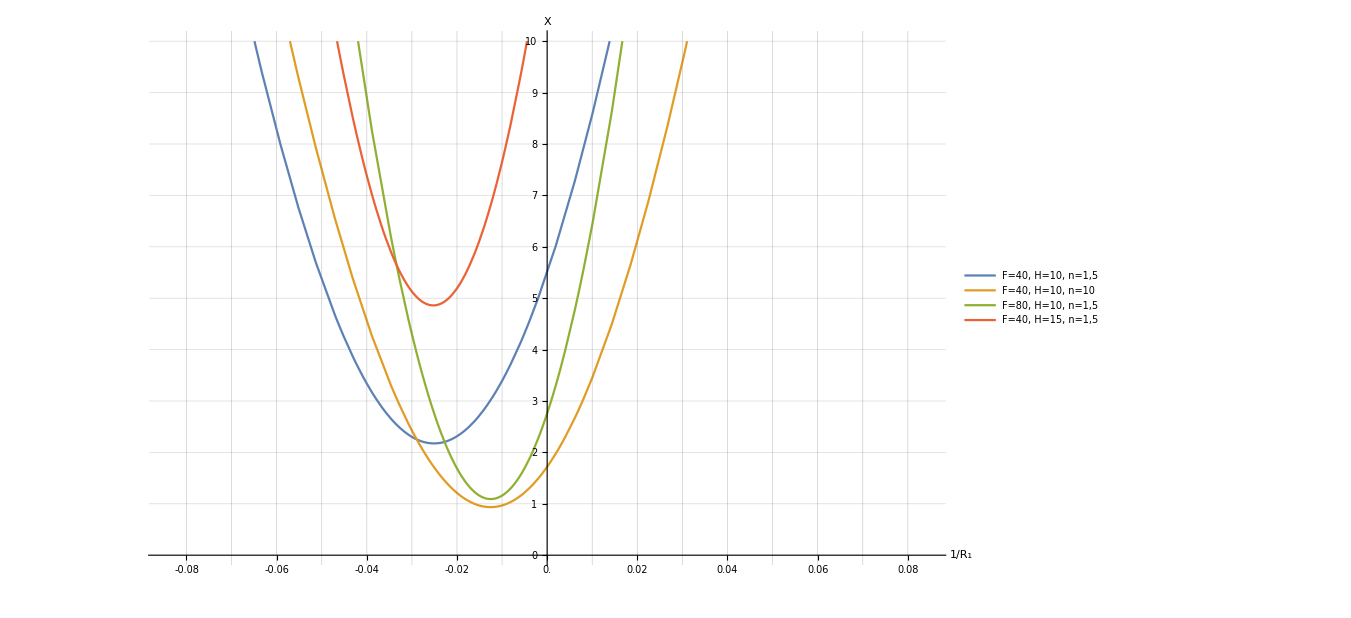

```mathematica
Show[
Plot[{
80+5 Cot[ArcSin[5 (0.05+r1)]+ArcSin[1.5 Sin[ArcSin[5 r1]-ArcSin[5 (0.05+r1)]-ArcSin[0.6666666666666666 Sin[ArcSin[5 r1]-ArcTan[1/16]]]]]],
80+5 Cot[ArcSin[5 (1/40+r1)]+ArcSin[2 Sin[ArcSin[5 r1]-ArcSin[5 (1/40+r1)]-ArcSin[1/2 Sin[ArcSin[5 r1]-ArcTan[1/16]]]]]],
160+5 Cot[ArcSin[5 (0.025+r1)]+ArcSin[1.5 Sin[ArcSin[5 r1]-ArcSin[5 (0.025+r1)]-ArcSin[0.6666666666666666 Sin[ArcSin[5 r1]-ArcTan[1/32]]]]]],
80+15/2 Cot[ArcSin[15/2 (0.05+r1)]+ArcSin[1.5 Sin[ArcSin[(15 r1)/2]-ArcSin[15/2 (0.05+r1)]-ArcSin[0.6666666666666666 Sin[ArcSin[(15 r1)/2]-ArcTan[3/32]]]]]]

},
{r1,-0.1,0.1},PlotRange->{{-0.085,0.085},{0,10}},GridLines->{Range[-0.1,0.1,0.01], Range[0,20,0.5]},
Ticks->{Range[-0.1,0.1,0.02],Range[0,10,1]},
ImageSize->1000,
AxesLabel->{Style["1/R_1",18],Style["X",18]},
AxesStyle->Directive[Arrowheads[0.02],Black],
LabelStyle->Black,
PlotLegends->Placed[
LineLegend[
Automatic,
{"F=40, H=10, n=1,5","F=40, H=10, n=10","F=80, H=10, n=1,5","F=40, H=15, n=1,5"},
LabelStyle->20,
LegendFunction->frame
],
{Scaled[0.8],Scaled[0.6]}
]
]

]
```